```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab9\lab9\lab9

```mathematica
num = Import["test2.txt","Table"]
```

{{1,0.999997,0.999994,0.999991,0.99999,0.999989,0.99999,0.999991,0.999994,0.999997,1},{1.1,1.1,1.09999,1.09999,1.09999,1.09999,1.09999,1.09999,1.09999,1.1,1.1},{1.2,1.2,1.19999,1.19999,1.19999,1.19999,1.19999,1.19999,1.19999,1.2,1.2},{1.3,1.3,1.29999,1.29999,1.29999,1.29999,1.29999,1.29999,1.29999,1.3,1.3},{1.4,1.4,1.39999,1.39999,1.39999,1.39999,1.39999,1.39999,1.39999,1.4,1.4},{1.5,1.5,1.49999,1.49999,1.49999,1.49999,1.49999,1.49999,1.49999,1.5,1.5},{1.6,1.6,1.59999,1.59999,1.59999,1.59999,1.59999,1.59999,1.59999,1.6,1.6},{1.7,1.7,1.69999,1.69999,1.69999,1.69999,1.69999,1.69999,1.69999,1.7,1.7},{1.8,1.8,1.79999,1.79999,1.79999,1.79999,1.79999,1.79999,1.79999,1.8,1.8},{1.9,1.9,1.89999,1.89999,1.89999,1.89999,1.89999,1.89999,1.89999,1.9,1.9},{2,2,1.99999,1.99999,1.99999,1.99999,1.99999,1.99999,1.99999,2,2}}

```mathematica
true = Table[1+j*0.1,{i,0,1/0.1},{j,0,1/0.1}] //Transpose
```

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1},{1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2},{1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3},{1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4},{1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5},{1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6},{1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7},{1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8},{1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9},{2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.}}

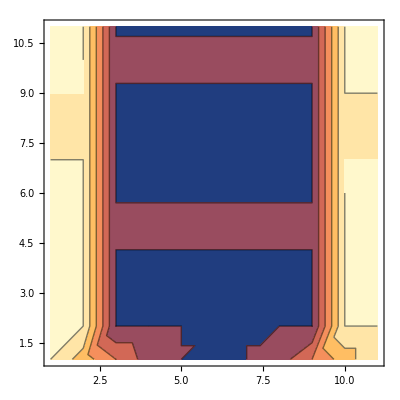

```mathematica
ListContourPlot[num-true]
```

```mathematica
g = Show[ListPlot3D[num,PlotRange->{{1,10},{1,10},{0.9,2.01}},PlotLegends->{{ "Численное решение"}}],ListPlot3D[true,PlotStyle->Blue,PlotLegends->{{ "Истинное решение"}}],ImageSize->600]
```

-Graphics3D-

```mathematica
ListContourPlot3D[true]
```

Visualization`Core`ListContourPlot3D::gmat1: Data value {{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«1»},{1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,«1»},{1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2,«1»},{1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3,«1»},«3»,{1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,«1»},{1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,«1»},{1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,«1»},«1»} must be a list of points of dimension 3.

ListContourPlot3D[{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1},{1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2,1.2},{1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3,1.3},{1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4},{1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5,1.5},{1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6},{1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7},{1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8,1.8},{1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.9},{2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.}}]

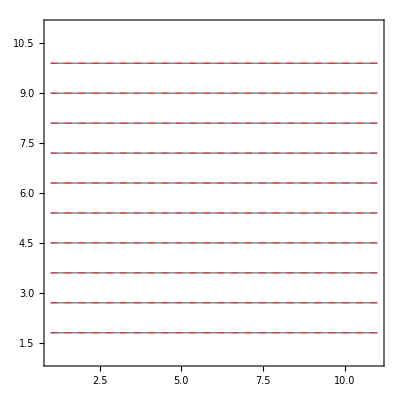

```mathematica
g=Show[ListContourPlot[num,ContourShading->None,Contours->10],ListContourPlot[true,ContourShading->None,ContourStyle->Directive[{Red,Dashed}],Contours->10]]
```

```mathematica
Export["test2.png",g]
```

test2.png